```mathematica
ClearAll["Global`*"]
Φ[x_,y_]=L/2(x-y)^2+f[y]-f[xs];
ρ[x_]:=1/(1+x/L);
yk1=xk-1/L g[xk];
βk=(√L-√m)/(√L+√m); (* m corresponds to μ tilde k in the paper*)
xk1=yk1+βk (yk1-yk);
ineq1=f[yk1]-f[xk]+g[yk1]*(xk-yk1)+1/(2L)(g[xk]-g[yk1])^2; (* all inequalities in the form "...<=0"*)
λ1=ρ[m];
ineq2=f[xk]-f[yk]+g[xk]*(yk-xk);
λ2=ρ[m];
ineq3=2 m (f[yk1]-f[xs])-g[yk1]^2;
λ3=(1-ρ[m])/(2  m);
expr1=λ1 ineq1 + λ2 ineq2 +λ3 ineq3;
expr2=Φ[xk1,yk1]-ρ[m] Φ[xk,yk]+ (4 L^2 √(m/L)-L(m-2m √(m/L))-m^2)/(2L^2(L+m)(√(m/L)+1)^2)(g[xk]+L(yk-xk))^2;
expr0=FullSimplify[expr1-expr2,Assumptions->{L>0}]
```

0

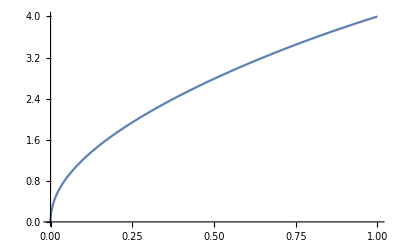

```mathematica
Plot[4Sqrt[x]-(x-2x Sqrt[x]) -x^2,{x,0,1}]
```